## 1st Nov 2018 on crest

```mathematica
datraw20181101 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\01\\qscan20181101-160720.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181101[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181101[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181101[[All,{5,7,13}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is VC laser brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 2nd Nov 2018 on crest

```mathematica
datraw20181102 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\02\\QE scan\\qscan20181102-092138.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181102[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181102[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181102[[All,{5,7,13}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is VC laser brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffpwer =datraw20181102[[All,11]]-datraw20181101[[All,11]];
```

```mathematica
diffpwrdat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffpwer}];
```

```mathematica
plot = ListPointPlot3D[diffpwrdat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is difference \n in laser power from 1st to 2nd Nov '18",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

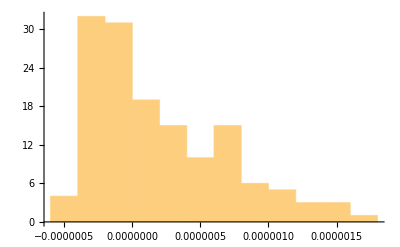

```mathematica
Histogram [diffpwer]
```

```mathematica
Mean[diffpwer]
```

1.97354×10^-7

## 9th November 2018 on crest

```mathematica
datraw20181109a = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\09\\qscan20181109-085332.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181109a[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181109a[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
datraw20181109b = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\09\\qscan0915merged.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181109b[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 13th November on crest

```mathematica
datraw20181113 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\13\\qscan20181113-162002.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181113[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181109a[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
datraw20181109b = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\09\\qscan0915merged.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181109b[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## !!2019!! 14th Jan (gun phase = ?)

```mathematica
datraw20190114 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\01\\14\\qscan20190114-125000.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190114[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 17 th Jan 2019 on crest

```mathematica
datraw20190117 = Import["W:\\qscan\\qscan20190117-190731.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190117[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 28 th Jan 2019 on crest

```mathematica
datraw20190128 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\01\\28\\qscan20190128-185812.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190128[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20190128[[All,9]]-datraw20190117[[All,9]]);
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
diffchargedat = Transpose[{datraw20190128[[All,5]],datraw20190117[[All,7]],diffcharge}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge difference \n 17th to 28th Jan in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[Transpose[{{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.},Symbol[],{46.5928-Symbol[],75.3662-Symbol[],75.2485-Symbol[],63.7706-Symbol[],75.4315-Symbol[],97.237-Symbol[],101.682-Symbol[],108.833-Symbol[],104.832-Symbol[],99.7078-Symbol[],92.8446-Symbol[],66.2544-Symbol[],98.1914-Symbol[],126.389-Symbol[],141.096-Symbol[],133.527-Symbol[],121.134-Symbol[],103.002-Symbol[],97.7992-Symbol[],84.1773-Symbol[],85.6937-Symbol[],88.7658-Symbol[],86.2428-Symbol[],77.9023-Symbol[],83.6021-Symbol[],96.6357-Symbol[],87.4586-Symbol[],93.4067-Symbol[],95.0277-Symbol[],110.349-Symbol[],118.493-Symbol[],126.167-Symbol[],135.109-Symbol[],145.672-Symbol[],144.339-Symbol[],84.2557-Symbol[],109.865-Symbol[],126.507-Symbol[],137.331-Symbol[],130.089-Symbol[],124.677-Symbol[],101.63-Symbol[],92.4262-Symbol[],90.6222-Symbol[],90.8183-Symbol[],92.6223-Symbol[],86.3212-Symbol[],80.0985-Symbol[],75.693-Symbol[],81.1444-Symbol[],88.5044-Symbol[],92.6616-Symbol[],95.0931-Symbol[],98.4005-Symbol[],123.487-Symbol[],131.383-Symbol[],132.847-Symbol[],141.293-Symbol[],133.867-Symbol[],103.146-Symbol[],115.134-Symbol[],136.495-Symbol[],142.09-Symbol[],140.077-Symbol[],125.684-Symbol[],130.795-Symbol[],110.271-Symbol[],105.068-Symbol[],98.6358-Symbol[],83.6413-Symbol[],70.4246-Symbol[],58.816-Symbol[],68.0454-Symbol[],71.9019-Symbol[],94.4787-Symbol[],111.526-Symbol[],115.97-Symbol[],128.403-Symbol[],148.038-Symbol[],139.266-Symbol[],144.155-Symbol[],139.397-Symbol[],104.244-Symbol[],88.6613-Symbol[],73.8105-Symbol[],117.225-Symbol[],121.134-Symbol[],146.744-Symbol[],147.149-Symbol[],170.759-Symbol[],128.468-Symbol[],115.225-Symbol[],107.486-Symbol[],82.9615-Symbol[],77.5232-Symbol[],65.3262-Symbol[],73.6275-Symbol[],81.968-Symbol[],98.3875-Symbol[],108.767-Symbol[],118.402-Symbol[],144.012-Symbol[],162.81-Symbol[],142.064-Symbol[],103.983-Symbol[],91.0928-Symbol[],72.647-Symbol[],22.6303-Symbol[],24.6043-Symbol[],51.4037-Symbol[],62.6724-Symbol[],89.3018-Symbol[],107.983-Symbol[],119.84-Symbol[],126.311-Symbol[],120.088-Symbol[],114.088-Symbol[],80.5169-Symbol[],84.0858-Symbol[],74.9086-Symbol[],58.7506-Symbol[],89.9816-Symbol[],93.7989-Symbol[],99.1718-Symbol[],103.577-Symbol[],114.624-Symbol[],90.8052-Symbol[],59.8487-Symbol[],63.5483-Symbol[],31.546-Symbol[],19.9373-Symbol[],11.6753-Symbol[],4.10611-Symbol[],5.24344-Symbol[],10.7863-Symbol[],26.2123-Symbol[],44.0044-Symbol[],65.2347-Symbol[],76.8696-Symbol[],82.0595-Symbol[],76.229-Symbol[],64.8033-Symbol[],54.4104-Symbol[],57.8224-Symbol[]}}],ColorFunction→Rainbow,PlotLabel→Colour is charge difference 
 17th to 28th Jan in pC,AxesLabel→{VC x (mm),VC y (mm)},AxesStyle→15,ViewPoint→{0,0,∞},PlotLegends→True,PlotStyle→PointSize[0.03]]

## 4 th March 2019 on crest

```mathematica
datraw20190304 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\03\\04\\qscan20190304-111110.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190304[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20190304[[All,9]]-datraw20190128[[All,9]]);
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
diffchargedat = Transpose[{datraw20190304[[All,5]],datraw20190128[[All,7]],diffcharge}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge difference \n 28thJan19 to 04thMar19 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[Transpose[{{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.},Symbol[],{0.878512-Symbol[],1.04373-Symbol[],2.82442-Symbol[],6.41896-Symbol[],9.41799-Symbol[],13.3577-Symbol[],14.1898-Symbol[],13.4137-Symbol[],14.4445-Symbol[],8.80348-Symbol[],6.6303-Symbol[],1.25476-Symbol[],13.6178-Symbol[],19.1618-Symbol[],26.6757-Symbol[],27.5432-Symbol[],27.9904-Symbol[],28.6994-Symbol[],25.2552-Symbol[],24.1891-Symbol[],17.3678-Symbol[],16.6004-Symbol[],13.7053-Symbol[],1.70901-Symbol[],24.0003-Symbol[],37.5468-Symbol[],40.8392-Symbol[],44.2955-Symbol[],44.947-Symbol[],48.5342-Symbol[],54.5795-Symbol[],53.5779-Symbol[],51.7038-Symbol[],48.3092-Symbol[],43.0078-Symbol[],26.639-Symbol[],57.3192-Symbol[],56.7864-Symbol[],71.5592-Symbol[],71.8916-Symbol[],68.0382-Symbol[],58.5866-Symbol[],53.1902-Symbol[],54.9907-Symbol[],56.4468-Symbol[],54.2768-Symbol[],48.418-Symbol[],32.2173-Symbol[],36.3644-Symbol[],48.5869-Symbol[],58.7312-Symbol[],60.7235-Symbol[],51.9422-Symbol[],59.372-Symbol[],61.3795-Symbol[],77.0754-Symbol[],72.689-Symbol[],79.6338-Symbol[],67.1595-Symbol[],45.07-Symbol[],75.0936-Symbol[],85.892-Symbol[],85.361-Symbol[],76.8182-Symbol[],68.6883-Symbol[],61.5483-Symbol[],52.0497-Symbol[],50.7088-Symbol[],64.2058-Symbol[],62.3632-Symbol[],53.8439-Symbol[],32.3851-Symbol[],41.5303-Symbol[],54.193-Symbol[],60.558-Symbol[],53.2991-Symbol[],49.9752-Symbol[],49.5745-Symbol[],53.4906-Symbol[],62.9043-Symbol[],79.3121-Symbol[],82.0703-Symbol[],86.8116-Symbol[],55.956-Symbol[],65.6936-Symbol[],89.2628-Symbol[],86.7754-Symbol[],68.0926-Symbol[],56.4718-Symbol[],53.0684-Symbol[],44.2777-Symbol[],49.5465-Symbol[],54.7574-Symbol[],53.5271-Symbol[],49.6792-Symbol[],41.0254-Symbol[],38.8724-Symbol[],51.1615-Symbol[],49.8596-Symbol[],48.0344-Symbol[],46.4135-Symbol[],53.7836-Symbol[],59.561-Symbol[],75.3589-Symbol[],89.0373-Symbol[],92.0752-Symbol[],81.9521-Symbol[],56.9418-Symbol[],45.5917-Symbol[],79.5519-Symbol[],98.0168-Symbol[],95.2517-Symbol[],78.824-Symbol[],70.7246-Symbol[],57.3507-Symbol[],56.1891-Symbol[],57.1053-Symbol[],55.9338-Symbol[],44.8029-Symbol[],38.8296-Symbol[],33.7447-Symbol[],54.6093-Symbol[],74.0803-Symbol[],75.0617-Symbol[],70.781-Symbol[],74.0397-Symbol[],86.4112-Symbol[],91.9737-Symbol[],74.1609-Symbol[],53.2652-Symbol[],48.2597-Symbol[],34.698-Symbol[],14.613-Symbol[],32.0536-Symbol[],43.8524-Symbol[],57.2174-Symbol[],71.0899-Symbol[],98.2906-Symbol[],81.4465-Symbol[],78.5104-Symbol[],75.428-Symbol[],70.8497-Symbol[],56.5637-Symbol[],34.0073-Symbol[]}}],ColorFunction→Rainbow,PlotLabel→Colour is charge difference 
 28thJan19 to 04thMar19 in pC,AxesLabel→{VC x (mm),VC y (mm)},AxesStyle→15,ViewPoint→{0,0,∞},PlotLegends→True,PlotStyle→PointSize[0.03]]

## 8 th March 2019 on crest

```mathematica
datraw20190308 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\03\\08\\qscan20190308-124749.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190308[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20190308[[All,9]]-datraw20190304[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20190308[[All,5]],datraw20190304[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge difference \n 04thMar19 to 08thMar19 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 14 th March 2019 laser work 1st scan INSTANTEOUS VALUES

```mathematica
datraw20190314a = Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190314-113515.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190314a[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser power Joules",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190314a[[All,{5,7,13}]], ColorFunction->"Rainbow",PlotLabel->Style["VC Brightness PixelCount",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

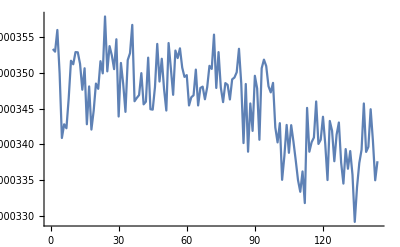

```mathematica
ListPlot[Flatten@datraw20190314a[[All,{11}]],Joined->True]
```

## 14 th March 2019 laser work 2nd scan

```mathematica
datraw20190414b = Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190314-140352.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190414b[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser power J",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190414b[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC Brightness PixelCount",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

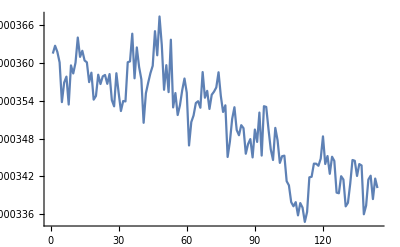

```mathematica
ListPlot[Flatten@datraw20190414b[[All,{14}]],Joined->True]
```

## 15 th March 2019 scan without aperture

```mathematica
datraw20190315a = Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190315-101757.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190315a[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Charge PC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315a[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser Energy J",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315a[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315a[[All,9]]/datraw20190315a[[All,14]];
ratioQbyE = Transpose[{datraw20190315a[[All,5]],datraw20190315a[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 15 th March 2019 scan with aperture

```mathematica
datraw20190315b= Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190315-132512.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190315b[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Charge PC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315b[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser Energy J",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315b[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 15 th March VC images Aperture In/Out

I don' t quite understand/remember the sequence of these plots in time. Seems I’ve got aperture in, then aperture out images. The aperture was probably taken out at end of shift as there was a shift on 16th march with beam.

```mathematica
vcimagefiles = FileNames["\\\\claraserv3\\CameraImages\\2019\\3\\15\\*"]
```

{\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_13-24-50_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-2-11_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-2-53_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-5-7_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-6-0_1images.hdf5}

```mathematica
alldat = Import[#,"Data"]  &/@  vcimagefiles;
MatrixPlot[#[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,500}]]&),ColorFunctionScaling->False,ImageSize->500] &/@ alldat
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[alldat[[3]][[1]][[800;;1400,900;;1700]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{50,2000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

```mathematica
MatrixPlot[alldat[[5]][[1]][[900;;1500,700;;1500]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{50,2000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

## 27 th March 2019 CATHODE REMOVED, APERTURE IN

```mathematica
datraw20190327a= Import["C:\\Users\\fj38.CLRC\\Documents\\GitHub\\Software\\Apps\\qscan\\qscan20190327-122133.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 1 in laser transport (uJ)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,26}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## Summary

```mathematica
dates = {1,2,9,13}
```

{1,2,9,13}

```mathematica
maxcharges = Max[#[[All,9]]] &/@ {datraw20181101 ,datraw20181102,datraw20181109,datraw20181113}
```

{183.442,158.189,100.074,90.8967}

```mathematica
maxPlas = Max[#[[All,11]]] &/@ {datraw20181101 ,datraw20181102,datraw20181109,datraw20181113}
```

{9.46534×10^-6,9.26804×10^-6,7.303×10^-6,6.71789×10^-6}

```mathematica
ratio = maxcharges/maxPlas
```

{1.93804×10^7,1.70682×10^7,1.37031×10^7,1.35306×10^7}

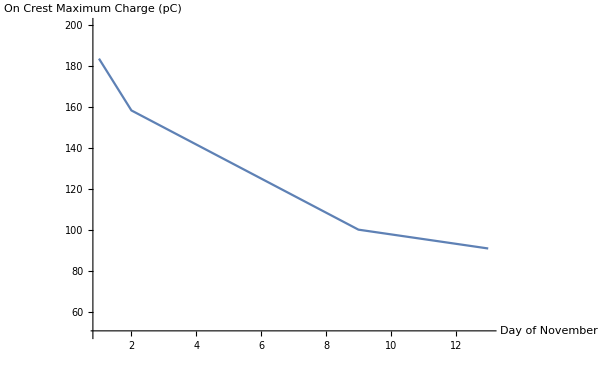

```mathematica
ListPlot[Transpose[{dates,maxcharges}],PlotRange->{All,{50,200}},Joined->True,AxesLabel->{"Day of November","On Crest Maximum Charge (pC)"},AxesStyle->15,ImageSize->600]
```

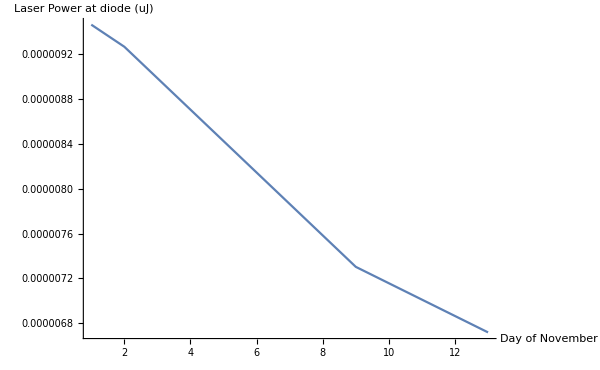

```mathematica
ListPlot[Transpose[{dates,maxPlas}],PlotRange->{All,All},Joined->True,AxesLabel->{"Day of November","Laser Power at diode (uJ)"},AxesStyle->15,ImageSize->600]
```

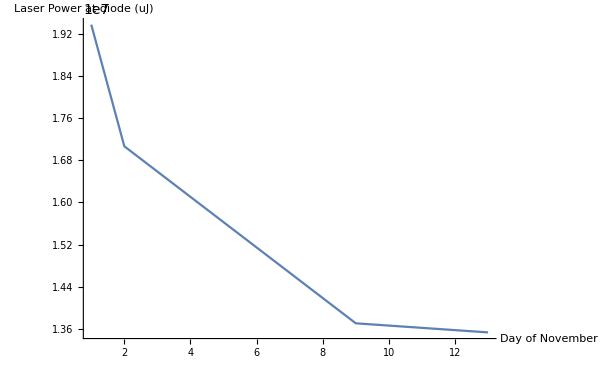

```mathematica
ListPlot[Transpose[{dates,ratio}],PlotRange->{All,All},Joined->True,AxesLabel->{"Day of November","Laser Power at diode (uJ)"},AxesStyle->15,ImageSize->600]
```